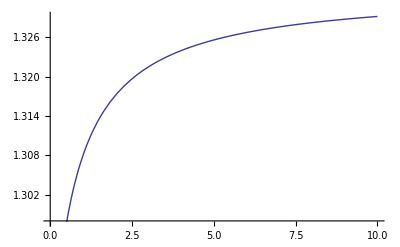

```mathematica
shear=3/2;
kappa2=2(2-shear);
a[Q_]=ArcCos[Q/(1+Q)];
f[Q_]=1/(Sqrt[Q]a[Q]);
rho[z_,Q_]=(1+Q)Cos[a[Q]*z]-Q;
sigma[Q_]:=2Integrate[rho[z,Q],{z,0,1}]
Plot[sigma[Q],{Q,0.01,10}]
```

```mathematica
k1[kx_,beta_,Q_]=(-4/a[Q]^2)(kx^2+2*shear*beta*Q/f[Q]^2);
k2[kx_,beta_,Q_]=-4*shear*beta*(1+Q)/(a[Q]^2f[Q]^2);
Ms1p[kx_,beta_,Q_]=MathieuSPrime[k1[kx,beta,Q],k2[kx,beta,Q],a[Q]/2];
Mc1p[kx_,beta_,Q_]=MathieuCPrime[k1[kx,beta,Q],k2[kx,beta,Q],a[Q]/2];
ya[zhat_,kx_,beta_,Q_]=MathieuC[k1[kx,beta,Q],k2[kx,beta,Q],zhat];
yb[zhat_,kx_,beta_,Q_]=MathieuC[k1[kx,beta,Q],k2[kx,beta,Q],zhat]Ms1p[kx,beta,Q]/Mc1p[kx,beta,Q]-MathieuS[k1[kx,beta,Q],k2[kx,beta,Q],zhat];
(*kx1=1;beta1=10;Q1=0.1;
Plot[{Abs[yb[zhat,kx1,beta1,Q1]]},{zhat,0,a[Q1]/2}]*)
```

```mathematica
wrontemp[zhat_,kx_,beta_,Q_]=Wronskian[{ya[zhat,kx,beta,Q],yb[zhat,kx,beta,Q]},zhat];
wron[kx_,beta_,Q_]=wrontemp[0.0,kx,beta,Q];(*wronskian is const wrt z*)
the1[zhat_,zeta_,kx_,beta_,Q_]=rho[2zhat/a[Q],Q]yb[zhat,kx,beta,Q]*ya[zeta,kx,beta,Q]rho[2zeta/a[Q],Q]Boole[zhat≥ zeta];
the2[zhat_,zeta_,kx_,beta_,Q_]=rho[2zhat/a[Q],Q]ya[zhat,kx,beta,Q]*yb[zeta,kx,beta,Q]rho[2zeta/a[Q],Q]Boole[zhat≤  zeta];
theta[kx_,beta_,Q_]:=(NIntegrate[the1[zhat,zeta,kx,beta,Q],{zhat,0,a[Q]/2},{zeta,0,a[Q]/2}]+NIntegrate[the2[zhat,zeta,kx,beta,Q],{zhat,0,a[Q]/2},{zeta,0,a[Q]/2}])/wron[kx,beta,Q];
theta[2,10,0.1]
```

0.330273-4.60743×10^-15 ⅈ

```mathematica
test[kx_,beta_,Q_]:=(a[Q]^3f[Q]^2/(8beta*theta[kx,beta,Q]))*sigma[Q]/(4*shear);
```

```mathematica
test[1,10,0.15]
```

$Aborted

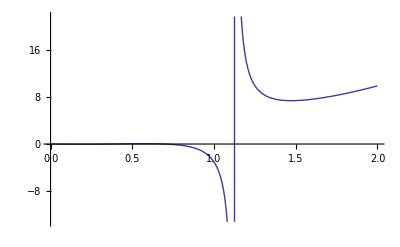

```mathematica
kxtilde[kx_,Q_]=Sqrt[1/(f[Q]^2Q)-kx^2];
bigF1[kx_,Q_]=(1+kx^2/kxtilde[kx,Q]^2)Sinc[kxtilde[kx,Q]]/(Cos[kxtilde[kx,Q]]-kxtilde[kx,Q]Sin[kxtilde[kx,Q]]/kx);
bigF2[kx_,Q_]=-kx^2/kxtilde[kx,Q]^2;
bigF3a[kx_,Q_]=f[Q]^2kx^2;
bigF3b[kx_,beta_,Q_]:=2(2shear+kappa2)/sigma[Q]-a[Q]^3f[Q]^2/(8beta theta[kx,beta,Q]);
bigF3bnomag[kx_,beta_,Q_]:=2(kappa2)/sigma[Q];
bigF[kx_,beta_,Q_]:=bigF1[kx,Q]+bigF2[kx,Q]+bigF3a[kx,Q]/bigF3b[kx,beta,Q];
bigFnomag[kx_,beta_,Q_]:=bigF1[kx,Q]+bigF2[kx,Q]+bigF3a[kx,Q]/bigF3bnomag[kx,beta,Q];
(*Plot[bigF[kx,0.1617783],{kx,.528,0.534},PlotRange->{-0.00005,0}]*)
Plot[bigFnomag[kx,10,0.15],{kx,0.0,2}]
```

```mathematica
bigF[0.55,17,0.15]
```

-0.000978237-5.58102×10^-16 ⅈ

```mathematica
4
```

4

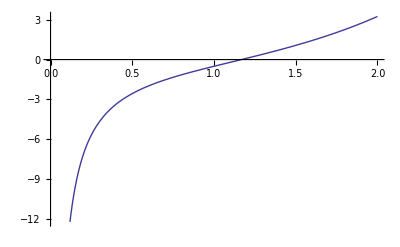

```mathematica
Q1=0.1;
Plot[Cos[kxtilde[kx,Q1]]-kxtilde[kx,Q1]Sin[kxtilde[kx,Q1]]/kx,{kx,0,2}]
```

```mathematica
N[kxtilde[kx,0.15]]
```

{{kx→-1.43999},{kx→1.43999}}

```mathematica
Pi/(1.1*64)
```

0.0446249